```mathematica
PtxZero = 10^-2;
Ptxi =10^-3;
a=4;
rD = 130;
rZero = 60;
rZeroD = 80;
n = 10^-11;
vZeroD=1;
vD=1;
vZero=1;
```

```mathematica
hZeroD=PtxZero/(rZeroD^a);
hD= Ptxi/(rD^a);
hZero = Ptxi/(rZero^a);
beta = (vZeroD*hZeroD)/(vD *hD);
```

```mathematica
gamma =1.2
```

1.2

```mathematica
Pd= Exp[-(gamma *n)/(vD *hD)];
PZero=Exp[-(gamma *n)/(vZero *hZero)];
G=1  (*10^(-10);*)
q=0.1;
qZero = 0.99
nUsers=50;
```

1

0.99

```mathematica
PZeroiZero[i_]:=PZero(1/(1+gamma))^(i-1)
```

```mathematica
PZeroiOne[i_]:= PZeroiZero[i](1+gamma* rZero^a* G)^-1
```

```mathematica
PDiZero[i_]:=Pd*(1/(1+gamma))^(i-1)
```

```mathematica
PDiOne[i_]:=PDiZero[i]/(1+(beta *gamma))
```

```mathematica
PZeroD[i_]:=Exp[-(gamma* n)/(vZero* hZero)](1/(1+gamma/beta))^i
```

```mathematica
rZeroF[k_,PrxOn_] :=PrxOn*∑_(i=k)^nUsers Binomial[  nUsers,i]*Binomial[i,k]*q^i *(1-q)^( nUsers-i)*PZeroiZero[i]^k*(1-PDiZero[i])^k*(1-PZeroiZero[i]*(1-PDiZero[i]))^(i-k)
rOneF[k_,PrxOn_, PtxOn_] := PrxOn*((1-qZero*PtxOn)*∑_(i=k)^nUsers Binomial[nUsers,i] *Binomial[i, k]*q^i *(1-q)^(nUsers-i)*PZeroiZero[i]^k*(1-PDiZero[i])^k*(1-PZeroiZero[i]*(1-PDiZero[i]))^(i-k)+ qZero*PtxOn*∑_(i=k)^nUsers Binomial[nUsers,i]*Binomial[i, k]*q^i *(1-q)^(nUsers-i)*PZeroiOne[i]^k*(1-PDiOne[i])^k*(1-PZeroiOne[i]*(1-PDiOne[i]))^(i-k))
```

```mathematica
pQueueDecreasedByOne[ PtxOn_] :=  qZero*PtxOn*∑_(k=0)^nUsers Binomial[nUsers,k] q^k *(1-q)^(nUsers-k)PZeroD[k]*(1-PZeroiOne[k](1-PDiOne[k]))^k
```

```mathematica
pQueueInreasedByOne[k_,PrxOn_, PtxOn_] :=PrxOn*((1-qZero*PtxOn)∑_(i=k)^nUsers Binomial[nUsers,i] Binomial[i, k] q^i*(1-q)^(nUsers-i)PZeroiZero[i]^k (1-PDiZero[i])^k(1-PZeroiZero[i](1-PDiZero[i]))^(i-k)+qZero*PtxOn*∑_(i=k)^nUsers Binomial[nUsers,i] Binomial[i, k] q^i*(1-q)^(nUsers-i)(1- PZeroD[i])PZeroiOne[i]^k(1-PDiOne[i])^k(1-PZeroiOne[i](1-PDiOne[i]))^(i-k)+qZero*PtxOn*∑_(i=k+1)^nUsers Binomial[nUsers,i] Binomial[i, k+1] q^i*(1-q)^(nUsers-i) PZeroD[i] PZeroiOne[i]^(k+1)(1-PDiOne[i])^(k+1)(1-PZeroiOne[i](1-PDiOne[i]))^(i-k-1))
```

```mathematica
pQueueInreasedByOneWhenZero[PrxOn_, PtxOn_] := 1-pQueueDecreasedByOne[ PtxOn]-∑_(i=1)^nUsers pQueueInreasedByOne[i,PrxOn, PtxOn]
```

```mathematica
pQueueInreasedByZero[k_, PrxOn_]:=PrxOn*∑_(i=k)^nUsers Binomial[nUsers,i] Binomial[i, k] q^i*(1-q)^(nUsers-i)PZeroiZero[i]^k *(1-PDiZero[i])^k*(1-PZeroiZero[i](1-PDiZero[i]))^(i-k)
```

```mathematica
lambdaZero[PrxOn_]:=∑_(k=1)^nUsers k  *rZeroF[k,PrxOn]
```

```mathematica
lambdaOne[PrxOn_, PtxOn_]:=∑_(k=1)^nUsers k* rOneF[k,PrxOn, PtxOn]
```

```mathematica
probQueueIsEmpty [PrxOn_, PtxOn_] :=(pQueueDecreasedByOne[ PtxOn] -∑_(i=1)^nUsers i *pQueueInreasedByOne[i,PrxOn, PtxOn] )/(pQueueDecreasedByOne[ PtxOn]-(∑_(i=1)^nUsers i *pQueueInreasedByOne[i,PrxOn, PtxOn])+lambdaZero [PrxOn])
probQueueIsEmpty [1, 0.5]
```

0.128453

```mathematica
avgQueueLength [PrxOn_, PtxOn_] :=1/(2(∑_(i=1)^nUsers i *pQueueInreasedByOne[i,PrxOn, PtxOn] -pQueueDecreasedByOne[PtxOn] )(pQueueDecreasedByOne[PtxOn]-(∑_(i=1)^nUsers i *pQueueInreasedByOne[i,PrxOn, PtxOn])+lambdaZero [PrxOn]))((∑_(i=1)^nUsers i *pQueueInreasedByOne[i,PrxOn, PtxOn] -pQueueDecreasedByOne[PtxOn] )(∑_(i=1)^nUsers i *(i+3)*pQueueInreasedByZero[i, PrxOn])+lambdaZero[PrxOn](2pQueueDecreasedByOne[ PtxOn]-∑_(i=1)^nUsers i *(i+3)*pQueueInreasedByOne[i,PrxOn, PtxOn]))
```

```mathematica
ThroughputDirect [PrxOn_,PtxOn_]:= (qZero *PtxOn *(1-probQueueIsEmpty[PrxOn, PtxOn])* ∑_(k=0)^(nUsers-1) Binomial[nUsers-1,k]*q^(k+1)*(1-q)^(nUsers-1-k)*PDiOne[k+1])+((1-qZero *PtxOn *(1-probQueueIsEmpty[PrxOn, PtxOn]))*∑_(k=0)^(nUsers-1) Binomial[nUsers-1,k]*q^(k+1)*(1-q)^(nUsers-1-k)*PDiZero[k+1])
```

```mathematica
ThroughputRelay[PrxOn_, PtxOn_] := PrxOn*((qZero *PtxOn *(1-probQueueIsEmpty[PrxOn, PtxOn]) *(∑_(k=0)^(nUsers-1) Binomial[nUsers-1,k]*q^(k+1)*(1-q)^(nUsers-1-k)* (1-PDiOne[k+1])*PZeroiOne[k+1]))+( (1-qZero* PtxOn *(1-probQueueIsEmpty[PrxOn, PtxOn])) *(∑_(k=0)^(nUsers-1) Binomial[nUsers-1,k]*q^(k+1)*(1-q)^(nUsers-1-k) *(1-PDiZero[k+1])*PZeroiZero[k+1])))
```

```mathematica
serviceRate[PtxOn_]:= PtxOn*∑_(k=0)^nUsers Binomial[nUsers,k]*qZero *q^k*(1-q)^(nUsers-k)*PZeroD[k]
```

```mathematica
(*Plot[serviceRate[p],{p,0,1}]*)
```

```mathematica
arrivalRate[PrxOn_, PtxOn_]:=  (lambdaZero[PrxOn] *PtxOn*probQueueIsEmpty[PrxOn, PtxOn] + PrxOn*(1-PtxOn ))+(lambdaOne[PrxOn, PtxOn]* PtxOn *(1-probQueueIsEmpty[PrxOn, PtxOn]))

arrivalRateNEW[PrxOn_, PtxOn_]:=  (lambdaZero[PrxOn] *probQueueIsEmpty[PrxOn, PtxOn] )+ (lambdaOne[PrxOn, PtxOn]* (1-probQueueIsEmpty[PrxOn, PtxOn]))
```

```mathematica
(*Plot3D[arrivalRate[Rx,Tx],{Rx,0,1},{Tx,0,1},AxesLabel->Automatic]*)
```

```mathematica
(*Plot3D[arrivalRateNEW[Rx,Tx],{Rx,0,1},{Tx,0,1},AxesLabel->Automatic]*)
```

```mathematica
nUsers
```

50

```mathematica
(*NMaximize[ {ThroughputDirect[PrxOn, PtxOn]+ThroughputRelay[PrxOn, PtxOn],serviceRate[PtxOn]≥ arrivalRateNEW[PrxOn, PtxOn] &&   PtxOn≥0 && PtxOn≤1  && PrxOn≥0 && PrxOn≤1},{PtxOn, PrxOn}]*)
```

```mathematica
(*gamma*)
```

```mathematica
TableForm[ results= Table[
{nUsers,Values[ NMaximize[ {ThroughputDirect[PrxOn, PtxOn]+ThroughputRelay[PrxOn, PtxOn],serviceRate[PtxOn]≥ arrivalRateNEW[PrxOn, PtxOn] &&   PtxOn≥0 && PtxOn≤1  && PrxOn≥0 && PrxOn≤1},{PtxOn, PrxOn}][[2]] ][[1]],
Values[ NMaximize[ {ThroughputDirect[PrxOn, PtxOn]+ThroughputRelay[PrxOn, PtxOn],serviceRate[PtxOn]≥ arrivalRateNEW[PrxOn, PtxOn] &&   PtxOn≥0 && PtxOn≤1  && PrxOn≥0 && PrxOn≤1},{PtxOn, PrxOn}][[2]] ][[2]],

NMaximize[ {ThroughputDirect[PrxOn, PtxOn]+ThroughputRelay[PrxOn, PtxOn],serviceRate[PtxOn]≥ arrivalRateNEW[PrxOn, PtxOn] &&   PtxOn≥0 && PtxOn≤1  && PrxOn≥0 && PrxOn≤1},{PtxOn, PrxOn}][[1]]
}, 
{nUsers,50} ] ];
```

```mathematica
TableForm[results,TableHeadings->{None,{"# Users","P(Tx=on)","P(Rx=on)","throughput/user"}}]
```

# Users | P(Tx=on) | P(Rx=on) | throughput/user
1 | 0.993775 | 1. | 0.086781
2 | 0.993775 | 1. | 0.07835
3 | 0.993775 | 1. | 0.0713268
4 | 0.993775 | 1. | 0.0653852
5 | 0.993775 | 1. | 0.0602925
6 | 0.993775 | 1. | 0.0558784
7 | 0.993775 | 1. | 0.0520152
8 | 0.993775 | 1. | 0.0486054
9 | 0.993775 | 1. | 0.0455732
10 | 0.993775 | 1. | 0.0428588
11 | 0.993775 | 1. | 0.0404143
12 | 0.993775 | 1. | 0.0382012
13 | 0.993775 | 1. | 0.0361878
14 | 0.993775 | 1. | 0.0343479
15 | 0.993775 | 1. | 0.0326599
16 | 0.993775 | 1. | 0.0311055
17 | 0.993775 | 1. | 0.0296692
18 | 0.993775 | 1. | 0.0283379
19 | 0.993775 | 1. | 0.0271003
20 | 0.993775 | 1. | 0.0259467
21 | 0.993775 | 1. | 0.0248687
22 | 0.993775 | 1. | 0.0238591
23 | 0.993775 | 1. | 0.0229113
24 | 0.993775 | 1. | 0.0220197
25 | 0.993775 | 1. | 0.0211795
26 | 0.993775 | 1. | 0.0203862
27 | 0.993775 | 1. | 0.0196358
28 | 0.993775 | 1. | 0.0189251
29 | 0.993775 | 1. | 0.0182507
30 | 0.993775 | 1. | 0.01761
31 | 0.993775 | 1. | 0.0170004
32 | 0.993775 | 1. | 0.0164197
33 | 0.993775 | 1. | 0.0158658
34 | 0.993775 | 1. | 0.0153369
35 | 0.993775 | 1. | 0.0148313
36 | 0.993775 | 1. | 0.0143475
37 | 0.993775 | 1. | 0.013884
38 | 0.993775 | 1. | 0.0134397
39 | 0.993775 | 1. | 0.0130132
40 | 0.993775 | 1. | 0.0126036
41 | 0.993775 | 1. | 0.0122099
42 | 0.993775 | 1. | 0.0118312
43 | 0.993775 | 1. | 0.0114665
44 | 0.993775 | 1. | 0.0111153
45 | 0.993775 | 1. | 0.0107767
46 | 0.993775 | 1. | 0.0104501
47 | 0.99348 | 1. | 0.0101348
48 | 0.99348 | 1. | 0.00983039
49 | 0.99348 | 1. | 0.00953624
50 | 0.991732 | 1. | 0.00925189

```mathematica
(*ListPointPlot3D[Table[ThroughputDirect[Rx,Tx],{Rx,0.01,1.0,0.01},{Tx,0.01,1.0,0.01}]]*)
```

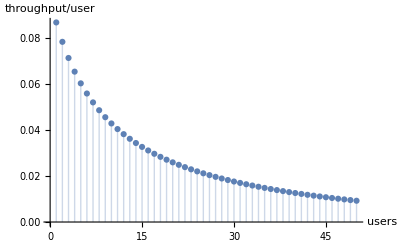

{0.554538,0.554538,0.554538,0.554538,0.554538,0.554538,0.554538,0.554538,0.554538,0.554538,0.554538,0.554538,0.554538,0.554538,0.554538,0.554538,0.554538,0.554538,0.554538,0.554538,0.554538,0.554538,0.554538,0.554538,0.554538,0.554538,0.554538,0.554538,0.554538,0.554538,0.554538,0.554538,0.554538,0.554538,0.554538,0.554538,0.554538,0.554538,0.554538,0.554538,0.554538,0.554538,0.554538,0.554538,0.554538,0.554538,0.554443,0.554443,0.554443,0.553879}

```mathematica
usersIdx=Table[results[[i,1]],{i,1,50}];
TxON = Table[results[[i,2]],{i,1,50}];RxON = Table[results[[i,3]],{i,1,50}];
perUserThroughput=Table[results[[i,4]],{i,1,50}];
ListPlot[Table[{usersIdx[[i]],perUserThroughput[[i]]},{i,1,50}], Filling->Axis, AxesLabel->{ users, throughput/user}]

avgQueueLength[TxON,RxON]
```

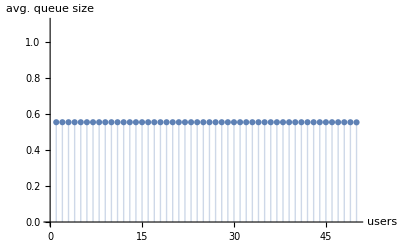

1

0.6

```mathematica
ListPlot[avgQueueLength[TxON,RxON],Filling->Axis, AxesLabel->{ users, "avg. queue size"}]
G
gamma
```

```mathematica
perUserThroughput
```

{0.086781,0.07835,0.0713268,0.0653852,0.0602925,0.0558784,0.0520152,0.0486054,0.0455732,0.0428588,0.0404143,0.0382012,0.0361878,0.0343479,0.0326599,0.0311055,0.0296692,0.0283379,0.0271003,0.0259467,0.0248687,0.0238591,0.0229113,0.0220197,0.0211795,0.0203862,0.0196358,0.0189251,0.0182507,0.01761,0.0170004,0.0164197,0.0158658,0.0153369,0.0148313,0.0143475,0.013884,0.0134397,0.0130132,0.0126036,0.0122099,0.0118312,0.0114665,0.0111153,0.0107767,0.0104501,0.0101348,0.00983039,0.00953624,0.00925189}

```mathematica
G, qZero
```

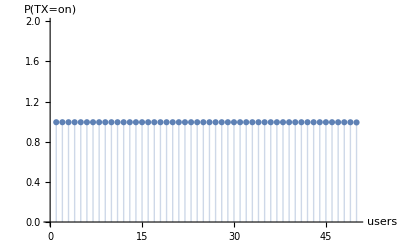

```mathematica
ListPlot[Table[{usersIdx[[i]],TxON[[i]]},{i,1,50}], Filling->Axis, AxesLabel->{ users, "P(TX=on)"}]
```

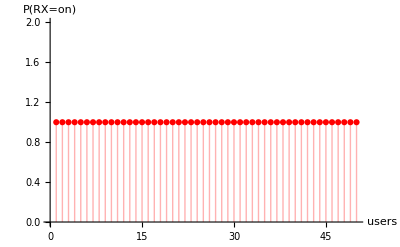

```mathematica
ListPlot[Table[{usersIdx[[i]],RxON[[i]]},{i,1,50}], Filling->Axis, AxesLabel->{ users, "P(RX=on)"},PlotStyle->{Red,Thick}]
```

```mathematica
gamma
```

0.6

```mathematica
G
```

1

```mathematica
TxON
```

{0.993775,0.993775,0.993775,0.993775,0.993775,0.993775,0.993775,0.993775,0.993775,0.993775,0.993775,0.993775,0.993775,0.993775,0.993775,0.993775,0.993775,0.993775,0.993775,0.993775,0.993775,0.993775,0.993775,0.993775,0.993775,0.993775,0.993775,0.993775,0.993775,0.993775,0.993775,0.993775,0.993775,0.993775,0.993775,0.993775,0.993775,0.993775,0.993775,0.993775,0.993775,0.993775,0.993775,0.993775,0.993775,0.993775,0.99348,0.99348,0.99348,0.991732}

```mathematica
RxON
```

{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}